```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
loadDumpSaves=True;
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
If[loadDumpSaves,NotebookEvaluate["modules/load_dump_saves.nb"]];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* For loop for calculating temperature curves *)
temps=Table[t,{t,0,1,0.1}];
tempData={};
dict=<|uq->"u",sq->"s",cq->"c",bq->"b"|>;

save=True;

For[iter=1,iter≤Length[temps],iter++,
temp=temps[[iter]];
ClearAll[J,P,FlavourSym,γMax,Λ,m1,m2,m3,ham,sM,t1,t2];
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
flavourSym=0;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=4;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
m1=uq;(* mass of quark 1 *)
m2=uq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=temp;
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)

(* all different masses = 0, two equal masses = 1, all equal masses = 2 *)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
(*Print["Time taken to compute t1: ", ToString[t1time]];*)
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
(*Print["Time taken to compute t2: ", ToString[t2time]];*)
DumpSave["modules/dumpSave/summationVariables.mx",summationVariables];
DumpSave["modules/dumpSave/talmi.mx",talmi];

(* Obtain projector matrix *)
proj=projector[states,flavourSym,case];

(* Required matrices for hamiltonian *)
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];
ham[ω_]:=Hb[ω,temperature,m1,m2,m3,proj];

(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,0.01,0.9,0.05]];
(*Print["Time taken to find minimum: ", ToString[minTime]];*)
wMin=(a+b)/2;
hamiltonian=ham[wMin];
eigvalMin=Eigenvalues[hamiltonian][[-excited-1]];
AppendTo[tempData,{temp,eigvalMin}];
Print[iter,". t = ", temp,", ω = ",wMin, ", E = ",eigvalMin];
(*Print["{ω_min, E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
Print["Number of basis functions (matrix size): ", Length[hamiltonian]];*)
(* Dump Saves *)

DumpSave["modules/dumpSave/nineJ.mx",nineJ];
DumpSave["modules/dumpSave/rel.mx",rel];
DumpSave["modules/dumpSave/Rcoeff.mx",Rcoeff];
DumpSave["modules/dumpSave/Lcoeff.mx",Lcoeff];
]
If[save,
temperatureData[J_,P_,flavourSym_,γMax_,Λ_,S_,m1_,m2_,m3_,excited_,tempData_]:=temperatureData[J,P,flavourSym,γMax,Λ,S,m1,m2,m3,excited]=tempData;
temperatureData[J,P,flavourSym,γMax,Λ,S,m1,m2,m3,excited,tempData];
DumpSave["temperature_data.mx",temperatureData];
Print["Saved temperature data successfully"]
];
```

1. t = 0., ω = 0.584849, E = 2.29291

2. t = 0.1, ω = 0.554196, E = 2.20896

3. t = 0.2, ω = 0.535251, E = 2.12239

4. t = 0.3, ω = 0.504598, E = 2.03288

5. t = 0.4, ω = 0.455, E = 1.93982

6. t = 0.5, ω = 0.424347, E = 1.84243

7. t = 0.6, ω = 0.374749, E = 1.73962

8. t = 0.7, ω = 0.325151, E = 1.62955

9. t = 0.8, ω = 0.275553, E = 1.509

10. t = 0.9, ω = 0.195301, E = 1.37016

11. t = 1., ω = 0.034799, E = 1.17263

Saved temperature data successfully

```mathematica
Get["temperature_data.mx"]
```

```mathematica
?temperatureData
```

```mathematica
pos=temperatureData[1/2,+1,0,4,0,1/2,uq,uq,cq,0]
neg=temperatureData[1/2,-1,0,4,1,1/2,uq,uq,cq,0]
```

{{0.,2.29291},{0.1,2.20896},{0.2,2.12239},{0.3,2.03288},{0.4,1.93982},{0.5,1.84243},{0.6,1.73962},{0.7,1.62955},{0.8,1.509},{0.9,1.37016},{1.,1.17263}}

{{0.,2.66773},{0.1,2.56241},{0.2,2.45314},{0.3,2.33991},{0.4,2.22161},{0.5,2.09693},{0.6,1.96456},{0.7,1.82136},{0.8,1.6626},{0.9,1.47624},{1.,1.19961}}

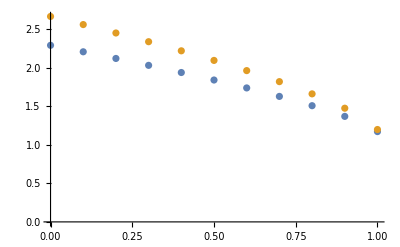

```mathematica
ListPlot[{pos,neg}]
```